```mathematica
(*BMP=1*) (*0.4, No CHIR with 0.1*)

aBS = 100;

aSW= 1/10; (*0.1*)
nSW=2;(*"TBX6 production rate"*)
KSW=155/100;(*Sqrt[10]Sqrt[5];*)

aWW=4331/10000;(*"CDX2 production rate"*)
nWW=3;(*"Bra production rate"*)
KWW=145/100;(*"Efficiency of TBX6 activation by BRA"*)

dW=467/10000;(*"Hill coefficient of TBX6 activation by BRA"*)

aWb = 168/100;
nWB = 25/10;
KWB = 59/100;

db =154/100;
```

```mathematica
(*BMP=1*) (*0.4, No CHIR with 0.1*)

(*aBS = 100;

aSW= 3/10; (*0.1*)
nSW=2;(*"TBX6 production rate"*)
KSW=Sqrt[10];(*Sqrt[10]Sqrt[5];*)

aWW=4/10;(*"CDX2 production rate"*)
nWW=2;(*"Bra production rate"*)
KWW=2.000000;(*"Efficiency of TBX6 activation by BRA"*)

dW=1/10;(*"Hill coefficient of TBX6 activation by BRA"*)

aWb = 5/10;
nWB = 3;
KWB = 3/10;

db =5/10;*)
```

```mathematica
dSMAD4dt[BMP_,SMAD4_,WRNA_,bCat_]:=aBS*(BMP-SMAD4);
dWRNAdt[BMP_,SMAD4_,WRNA_,bCat_]  :=((aSW*SMAD4^nSW)/(KSW^nSW+SMAD4^nSW))+((aWW*(bCat^nWW))/(KWW^nWW+bCat^nWW))-dW*WRNA;
dbCatdt[BMP_,SMAD4_,WRNA_,bCat_]:=((aWb*(WRNA^nWB))/(KWB^nWB+WRNA^nWB))-db*bCat;
```

```mathematica
Rts1[BMP0_]:=Module[{poly1,poly2,poly3,poly4,poly5,poly6,poly7,poly8,poly9,poly10,polys,polyeqn,soln,polls,i,reals,realsoln,ls2},
poly1 = dSMAD4dt[BMP,SMAD4,WRNA,bCat]/.{BMP->BMP0};
poly2=dWRNAdt[BMP,SMAD4,WRNA,bCat] /.{BMP->BMP0};
poly3=dbCatdt[BMP,SMAD4,WRNA,bCat] /.{BMP->BMP0};
polyeqn={poly1==0,poly2==0,poly3==0};
soln=NSolve[polyeqn,{SMAD4,WRNA,bCat},Reals];
ls=Array[2&,Length[soln]];
For[i=1,i<Length[soln]+1,i++,
ls[[i]]=If[Im[soln[[i]][[1]][[2]]]==0,1,0];
ls[[i]]=If[Im[soln[[i]][[2]][[2]]]==0,ls[[i]],0]
];
reals=Flatten[Position[ls,1]];
realsoln=soln[[reals]];
ls2={};
For[i=1,i<Length[realsoln]+1,i++,ls2=Join[ls2,{{SMAD4,WRNA,bCat}/.realsoln[[i]]}]];
ls2
]
```

```mathematica
Rts1[0.3]
```

{{0.3,2.72285,1.06758},{0.3,0.0773207,0.00674071},{0.3,0.613304,0.571847}}

```mathematica
Saddles[BMP0_]:=Module[{poly1,poly2,poly3,poly4,poly5,poly6,poly7,poly8,poly9,poly10,polys,H,Ro1,R2,i,Rsaddleinds,Imsaddleinds,deginds,Rmininds,Rmaxinds,Immininds,Immaxinds,SaddleH,DegH,NonDegH,NonEquilibrianorSaddle,j,realeigH,eigh},
Ro1=Rts1[BMP0];
poly1=dSMAD4dt[BMP,SMAD4,WRNA,bCat] /.{BMP->BMP0};
poly2 =dWRNAdt[BMP,SMAD4,WRNA,bCat] /.{BMP->BMP0};
poly3=dbCatdt[BMP,SMAD4,WRNA,bCat] /.{BMP->BMP0};
polys={poly1,poly2,poly3};
Rsaddleinds={};
Imsaddleinds = {};
deginds={};
Rmininds = {};
Immininds = {};
Rmaxinds = {};
Immaxinds = {};
For[i=1,i<Length[Ro1]+1,i++,
H = D[polys,{{SMAD4,WRNA,bCat},1}]/.{BMP->BMP0,SMAD4->Ro1[[i]][[1]],WRNA->Ro1[[i]][[2]],bCat-> Ro1[[i]][[3]]};
If[Det[H]==0,deginds=Join[deginds,{i}]];
(*If[Det[H]==0,DegH=Join[DegH,{Det[H]}]];*)
eigh = Eigenvalues[H];
If[(Re[eigh]==eigh)&&Det[H]≠0, (*real case*)
If[AllTrue[Re[eigh],Positive[#]&],Rmaxinds = Join[Rmaxinds,{i}],
If[AllTrue[Re[eigh],Negative[#]&],Rmininds = Join[Rmininds,{i}], Rsaddleinds = Join[Rsaddleinds,{i}]]], (*these are the critical points with real eigenvalues: maxima (Rmaxinds), minima(Rmininds) and saddles (Rsaddleinds)*)
If[AllTrue[Re[eigh],Positive[#]&],Immaxinds = Join[Immaxinds,{i}],
If[AllTrue[Re[eigh],Negative[#]&],Immininds = Join[Immininds,{i}], Imsaddleinds = Join[Imsaddleinds,{i}]]]](*these are the critical points with imaginary eigenvalues: maxima (Immaxinds), minima(Immininds) and saddles (Imsaddleinds)*)
(*If[!PositiveDefiniteMatrixQ[H]&&!PositiveDefiniteMatrixQ[-H]&&Det[H]≠0,SaddleH=Join[SaddleH,{Det[H]}];
];*)
];(*Complement gives the elements in Range[Length[R1]] that are not in saddleinds*) 
(*{{Ro1[[Rsaddleinds]]},{Ro1[[Join[Rmininds,Rmaxinds]]]},Ro1[[deginds]]}*)
{{Ro1[[Rsaddleinds]],Ro1[[Imsaddleinds]]},{Ro1[[Join[Rmininds,Rmaxinds]]],Ro1[[Join[Immininds,Immaxinds]]]},Ro1[[deginds]]}
(*{{R1[[saddleinds]],R1[[deginds]],R1[[notsaddleindsnordeg]]},{SaddleH ,DegH}}*)(*The first are the roots that are saddles and or degenerate, the others are the points that are not saddles*)
]
```

```mathematica
Saddles[0.3]
```

{{{{0.3,0.331513,0.574359}},{}},{{{0.3,0.0267597,0.000709203},{0.3,0.750417,0.939944}},{}},{}}

```mathematica
PositiveSaddles[BMP0_]:=Module[{poly1,poly2,poly3,poly4,poly5,poly6,poly7,poly8,poly9,poly10,polys,H,Ro1,R2,i,Rsaddleinds,Imsaddleinds,deginds,Rmininds,Rmaxinds,Immininds,Immaxinds,SaddleH,DegH,NonDegH,NonEquilibrianorSaddle,j,realeigH,eigh},
Ro1=Rts1[BMP0];
poly1=dSMAD4dt[BMP,SMAD4,WRNA,bCat] /.{BMP->BMP0};
poly2 =dWRNAdt[BMP,SMAD4,WRNA,bCat] /.{BMP->BMP0};
poly3=dbCatdt[BMP,SMAD4,WRNA,bCat] /.{BMP->BMP0};
polys={poly1,poly2,poly3};
Rsaddleinds={};
Imsaddleinds = {};
deginds={};
Rmininds = {};
Immininds = {};
Rmaxinds = {};
Immaxinds = {};
For[i=1,i<Length[Ro1]+1,i++,
H = D[polys,{{SMAD4,WRNA,bCat},1}]/.{BMP->BMP0,SMAD4->Ro1[[i]][[1]],WRNA->Ro1[[i]][[2]],bCat-> Ro1[[i]][[3]]};
If[Det[H]==0,deginds=Join[deginds,{i}]];
(*If[Det[H]==0,DegH=Join[DegH,{Det[H]}]];*)
eigh = Eigenvalues[H];
If[AllTrue[Ro1[[i]],Positive]&&(Re[eigh]==eigh)&&Det[H]≠0, (*real case*)
If[AllTrue[Re[eigh],Positive[#]&],Rmaxinds = Join[Rmaxinds,{i}],
If[AllTrue[Re[eigh],Negative[#]&],Rmininds = Join[Rmininds,{i}], Rsaddleinds = Join[Rsaddleinds,{i}]]], (*these are the critical points with real eigenvalues: maxima (Rmaxinds), minima(Rmininds) and saddles (Rsaddleinds)*)
If[AllTrue[Ro1[[i]],Positive],If[AllTrue[Re[eigh],Positive[#]&],Immaxinds = Join[Immaxinds,{i}],
If[AllTrue[Re[eigh],Negative[#]&],Immininds = Join[Immininds,{i}], Imsaddleinds = Join[Imsaddleinds,{i}]]]]](*these are the critical points with imaginary eigenvalues: maxima (Immaxinds), minima(Immininds) and saddles (Imsaddleinds)*)
(*If[!PositiveDefiniteMatrixQ[H]&&!PositiveDefiniteMatrixQ[-H]&&Det[H]≠0,SaddleH=Join[SaddleH,{Det[H]}];
];*)
];(*Complement gives the elements in Range[Length[R1]] that are not in saddleinds*) 
(*{{Ro1[[Rsaddleinds]]},{Ro1[[Join[Rmininds,Rmaxinds]]]},Ro1[[deginds]]}*)
{{Ro1[[Rsaddleinds]],Ro1[[Imsaddleinds]]},{Ro1[[Join[Rmininds,Rmaxinds]]],Ro1[[Join[Immininds,Immaxinds]]]},Ro1[[deginds]]}
(*{{R1[[saddleinds]],R1[[deginds]],R1[[notsaddleindsnordeg]]},{SaddleH ,DegH}}*)(*The first are the roots that are saddles and or degenerate, the others are the points that are not saddles*)
]
```

```mathematica
EquilibriaPlot2D[BMP0_,xmin_,xmax_,ymin_,ymax_]:=Module[{G,pt,wl,Rsad,Imsad,Rminmax,Imminmax,all,lev,i,pt1,pt2,pt3,deg,pt4,pt5,GenesNames,poly},
(*G=F2[x,y]/.{a->a0,b->b0,c->c0,L->L0};*)
GenesNames = {"SMAD4","WRNA","bCat"};
pt={};
all=Saddles[BMP0];
Rsad=all[[1]][[1]][[1;;All,{2,3}]];
Imsad = all[[1]][[2]][[1;;All,{2,3}]];
Rminmax = all[[2]][[1]][[1;;All,{2,3}]];
Imminmax = all[[2]][[2]][[1;;All,{2,3}]];
deg=all[[3]][[1;;All,{2,3}]];
pt={};
pt1 = {};
pt2={};
pt3={};
pt4={};
pt5={};
If[Rsad≠{},
pt1=ListPlot[Rsad,PlotStyle->{Orange,PointSize[Large]},AxesLabel->{GenesNames[[2]],GenesNames[[3]]}];
];
If[Imsad≠{},
pt2=ListPlot[Imsad,PlotStyle->{Magenta,PointSize[Large]},AxesLabel->{GenesNames[[2]],GenesNames[[3]]}];
];
If[Rminmax≠{},
pt3=ListPlot[Rminmax,PlotStyle->{Blue,PointSize[Large]},AxesLabel->{GenesNames[[2]],GenesNames[[3]]}];
];
If[Imminmax≠{},
pt4=ListPlot[Imminmax,PlotStyle->{Cyan,PointSize[Large]},AxesLabel->{GenesNames[[2]],GenesNames[[3]]}];
];
If[deg≠{},pt5=ListPointPlot3D[deg,PlotStyle->{Green,PointSize[Large]}]];
(*pt2=ListPlot[sad,PlotMarkers->{Automatic,Medium},PlotStyle->Red];*)
Show[Join[pt,{pt1,pt2,pt3,pt4,pt5}],Background->White,ImageSize->Large,PlotRange->{{xmin,xmax},{ymin,ymax}}]
]
```

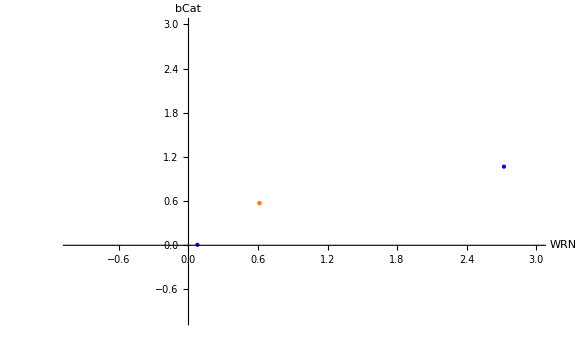

```mathematica
EquilibriaPlot2D[0.3,-1,3,-1,3]
```

## Bifurcation Set (Just WNT)

```mathematica
Rts1WRNA[BMP0_]:=(*This function computes the critical points of the function and only saves de WRNA coordinate. You could modify it so that it saves more than one coordinate*)Module[{poly1,poly2,poly3,poly4,poly5,poly6,poly7,poly8,poly9,poly10,polys,polyeqn,soln,polls,i,reals,realsoln,ls2},
poly1 = dSMAD4dt[BMP,SMAD4,WRNA,bCat]/.{BMP->BMP0};
poly2=dWRNAdt[BMP,SMAD4,WRNA,bCat] /.{BMP->BMP0};
poly3=dbCatdt[BMP,SMAD4,WRNA,bCat] /.{BMP->BMP0};
polyeqn={poly1==0,poly2==0,poly3==0};
soln=NSolve[polyeqn,{SMAD4,WRNA,bCat},Reals];
ls=Array[2&,Length[soln]];
For[i=1,i<Length[soln]+1,i++,
ls[[i]]=If[Im[soln[[i]][[1]][[2]]]==0,1,0];
ls[[i]]=If[Im[soln[[i]][[2]][[2]]]==0,ls[[i]],0]
];
reals=Flatten[Position[ls,1]];
realsoln=soln[[reals]];
ls2={};
For[i=1,i<Length[realsoln]+1,i++,ls2=Join[ls2,{WRNA/.realsoln[[i]]}]];
ls2
]
```

```mathematica
SaddlesWRNA[BMP0_]:=(*This function groups the critical points into subgroups depending on stability*)Module[{poly1,poly2,poly3,poly4,poly5,poly6,poly7,poly8,poly9,poly10,polys,H,Ro1,R2,i,Rsaddleinds,Imsaddleinds,deginds,Rmininds,Rmaxinds,Immininds,Immaxinds,SaddleH,DegH,NonDegH,NonEquilibrianorSaddle,j,realeigH,eigh,Ro1bcat},
Ro1=Rts1[BMP0];
Ro1bcat=Rts1WRNA[BMP0];
poly1=dSMAD4dt[BMP,SMAD4,WRNA,bCat] /.{BMP->BMP0};
poly2 =dWRNAdt[BMP,SMAD4,WRNA,bCat] /.{BMP->BMP0};
poly3=dbCatdt[BMP,SMAD4,WRNA,bCat] /.{BMP->BMP0};
polys={poly1,poly2,poly3};
Rsaddleinds={};
Imsaddleinds = {};
deginds={};
Rmininds = {};
Immininds = {};
Rmaxinds = {};
Immaxinds = {};
For[i=1,i<Length[Ro1]+1,i++,
H = D[polys,{{SMAD4,WRNA,bCat},1}]/.{BMP->BMP0,SMAD4->Ro1[[i]][[1]],WRNA->Ro1[[i]][[2]],bCat-> Ro1[[i]][[3]]};
If[Det[H]==0,deginds=Join[deginds,{i}]];
(*If[Det[H]==0,DegH=Join[DegH,{Det[H]}]];*)
eigh = Eigenvalues[H];
If[(Re[eigh]==eigh)&&Det[H]≠0, (*real case*)
If[AllTrue[Re[eigh],Positive[#]&],Rmaxinds = Join[Rmaxinds,{i}],
If[AllTrue[Re[eigh],Negative[#]&],Rmininds = Join[Rmininds,{i}], Rsaddleinds = Join[Rsaddleinds,{i}]]], (*these are the critical points with real eigenvalues: maxima (Rmaxinds), minima(Rmininds) and saddles (Rsaddleinds)*)
If[AllTrue[Re[eigh],Positive[#]&],Immaxinds = Join[Immaxinds,{i}],
If[AllTrue[Re[eigh],Negative[#]&],Immininds = Join[Immininds,{i}], Imsaddleinds = Join[Imsaddleinds,{i}]]]](*these are the critical points with imaginary eigenvalues: maxima (Immaxinds), minima(Immininds) and saddles (Imsaddleinds)*)
(*If[!PositiveDefiniteMatrixQ[H]&&!PositiveDefiniteMatrixQ[-H]&&Det[H]≠0,SaddleH=Join[SaddleH,{Det[H]}];
];*)
];(*Complement gives the elements in Range[Length[R1]] that are not in saddleinds*) 
(*{{Ro1[[Rsaddleinds]]},{Ro1[[Join[Rmininds,Rmaxinds]]]},Ro1[[deginds]]}*)
{{Ro1bcat[[Rsaddleinds]],Ro1bcat[[Imsaddleinds]]},{Ro1bcat[[Join[Rmininds,Rmaxinds]]],Ro1bcat[[Join[Immininds,Immaxinds]]]},Ro1bcat[[deginds]]}
(*{{R1[[saddleinds]],R1[[deginds]],R1[[notsaddleindsnordeg]]},{SaddleH ,DegH}}*)(*The first are the roots that are saddles and or degenerate, the others are the points that are not saddles*)
]
```

```mathematica
Rts1WRNA[0]
```

{0.711453,0,0.355516}

```mathematica
SaddlesWRNA[0]
```

{{{0.355516},{}},{{0.711453,0},{}},{}}

```mathematica
BifurcationSet[BMPmin_,BMPmax_,dBMP_]:= (*This plots the critical points in red if stable, black if unstable and blue if degenerate. You can modify this function to, instead of just saving and plotting the WRNA coordinate, it makes a 3D plot with two gene coordinates  *)Module[{RangeBMP,i,StablePointsList,UnstablePointsList,DegPointsList,CPS,j,pt,pt1,pt2,pt3},
RangeBMP = Range[BMPmin,BMPmax,dBMP];
StablePointsList = {};
UnstablePointsList = {};
DegPointsList = {};
For[i=1,i<Length[RangeBMP]+1,i++,
CPS = SaddlesWRNA[RangeBMP[[i]]];
If[Length[CPS[[1]][[1]]]>0, 
For[j=1,j<Length[CPS[[1]][[1]]]+1,j++,
UnstablePointsList = Join[UnstablePointsList,{{RangeBMP[[i]],CPS[[1]][[1]][[j]]}}]]];
If[Length[CPS[[2]][[1]]]>0, 
For[j=1,j<Length[CPS[[2]][[1]]]+1,j++,
StablePointsList = Join[StablePointsList,{{RangeBMP[[i]],CPS[[2]][[1]][[j]]}}]]];
If[Length[CPS[[3]]]>0, 
For[j=1,j<Length[CPS[[3]]]+1,j++,
DegPointsList = Join[DegPointsList,{RangeBMP[[i]],CPS[[3]][[j]]}]]];];
pt={};
pt1 = {};
pt2={};
pt3={};
If[UnstablePointsList≠{},
pt1=ListPlot[UnstablePointsList,PlotStyle->{Black,PointSize[0.005]},AxesLabel->{"BMP","bCat"}];
];
If[StablePointsList≠{},
pt2=ListPlot[StablePointsList,PlotStyle->{Red,PointSize[0.005]},AxesLabel->{"BMP","bCat"}];
];
If[DegPointsList≠{},
pt3=ListPlot[DegPointsList,PlotStyle->{Blue,PointSize[0.005]},AxesLabel->{"BMP","WP"}];
];
(*pt2=ListPlot[sad,PlotMarkers->{Automatic,Medium},PlotStyle->Red];*)
Show[Join[pt,{pt1,pt2,pt3}],Background->White,ImageSize->Large,PlotRange->All]
]
```

```mathematica
nSW=2;(*"TBX6 production rate"*)
KSW=Sqrt[10];(*Sqrt[10]Sqrt[5];*)
```

```mathematica
Rts1[0.3]
```

{{0.3,0.0267597,0.000709203},{0.3,0.750417,0.939944},{0.3,0.331513,0.574359}}

```mathematica
Rts1bCat[0.3]
```

{0.000709203,0.939944,0.574359}

```mathematica
Rts1bCat[0.1]
```

{9.97005×10^-7,0.619025,0.931482}

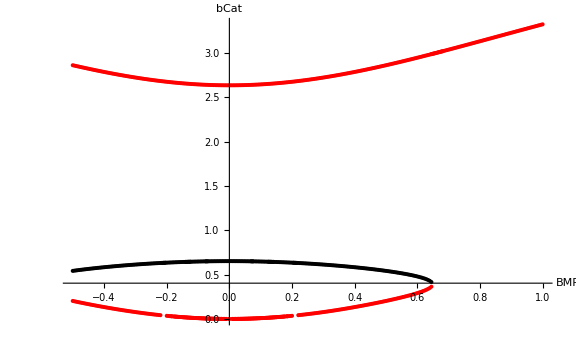

```mathematica
BifurcationSet[-0.5,1,0.005]
```

```mathematica
BifurcationSetDataWNT[BMPmin_,BMPmax_,dBMP_]:=Module[{RangeBMP,i,StablePointsList,UnstablePointsList,DegPointsList,CPS,j,pt,pt1,pt2,pt3},
RangeBMP = Range[BMPmin,BMPmax,dBMP];
StablePointsList = {};
UnstablePointsList = {};
DegPointsList = {};
For[i=1,i<Length[RangeBMP]+1,i++,
CPS = SaddlesWRNA[RangeBMP[[i]]];
If[Length[CPS[[1]][[1]]]>0, 
For[j=1,j<Length[CPS[[1]][[1]]]+1,j++,
UnstablePointsList = Join[UnstablePointsList,{{RangeBMP[[i]],CPS[[1]][[1]][[j]]}}]]];
If[Length[CPS[[2]][[1]]]>0, 
For[j=1,j<Length[CPS[[2]][[1]]]+1,j++,
StablePointsList = Join[StablePointsList,{{RangeBMP[[i]],CPS[[2]][[1]][[j]]}}]]];
If[Length[CPS[[3]]]>0, 
For[j=1,j<Length[CPS[[3]]]+1,j++,
DegPointsList = Join[DegPointsList,{RangeBMP[[i]],CPS[[3]][[j]]}]]];];
StablePointsList
]
```

```mathematica
Export["/Users/elenacamachoaguilar/Library/CloudStorage/Box-Box/WarmflashLab/Papers 2/BMPWNT_Elena/Supplemental-Information/Code/SignalingSystem/WNTSystem/StableBifPoints_WNT.dat",BifurcationSetDataWNT[-0.5,2,0.001],"TSV"]
```

/Users/elenacamachoaguilar/Library/CloudStorage/Box-Box/WarmflashLab/Papers 2/BMPWNT_Elena/Supplemental-Information/Code/SignalingSystem/WNTSystem/StableBifPoints_WNT.dat

```mathematica
BifurcationSetDataWNT[BMPmin_,BMPmax_,dBMP_]:=Module[{RangeBMP,i,StablePointsList,UnstablePointsList,DegPointsList,CPS,j,pt,pt1,pt2,pt3},
RangeBMP = Range[BMPmin,BMPmax,dBMP];
StablePointsList = {};
UnstablePointsList = {};
DegPointsList = {};
For[i=1,i<Length[RangeBMP]+1,i++,
CPS = SaddlesWRNA[RangeBMP[[i]]];
If[Length[CPS[[1]][[1]]]>0, 
For[j=1,j<Length[CPS[[1]][[1]]]+1,j++,
UnstablePointsList = Join[UnstablePointsList,{{RangeBMP[[i]],CPS[[1]][[1]][[j]]}}]]];
If[Length[CPS[[2]][[1]]]>0, 
For[j=1,j<Length[CPS[[2]][[1]]]+1,j++,
StablePointsList = Join[StablePointsList,{{RangeBMP[[i]],CPS[[2]][[1]][[j]]}}]]];
If[Length[CPS[[3]]]>0, 
For[j=1,j<Length[CPS[[3]]]+1,j++,
DegPointsList = Join[DegPointsList,{RangeBMP[[i]],CPS[[3]][[j]]}]]];];
UnstablePointsList
]
```

```mathematica
Export["/Users/elenacamachoaguilar/Library/CloudStorage/Box-Box/WarmflashLab/Papers 2/BMPWNT_Elena/Supplemental-Information/Code/SignalingSystem/WNTSystem/UnstableBifPoints_WNT.dat",BifurcationSetDataWNT[-0.5,2,0.001],"TSV"]
```

/Users/elenacamachoaguilar/Library/CloudStorage/Box-Box/WarmflashLab/Papers 2/BMPWNT_Elena/Supplemental-Information/Code/SignalingSystem/WNTSystem/UnstableBifPoints_WNT.dat

```mathematica
BifurcationSetDataWNT[BMPmin_,BMPmax_,dBMP_]:=Module[{RangeBMP,i,StablePointsList,UnstablePointsList,DegPointsList,CPS,j,pt,pt1,pt2,pt3},
RangeBMP = Range[BMPmin,BMPmax,dBMP];
StablePointsList = {};
UnstablePointsList = {};
DegPointsList = {};
For[i=1,i<Length[RangeBMP]+1,i++,
CPS = SaddlesWRNA[RangeBMP[[i]]];
If[Length[CPS[[1]][[1]]]>0, 
For[j=1,j<Length[CPS[[1]][[1]]]+1,j++,
UnstablePointsList = Join[UnstablePointsList,{{RangeBMP[[i]],CPS[[1]][[1]][[j]]}}]]];
If[Length[CPS[[2]][[1]]]>0, 
For[j=1,j<Length[CPS[[2]][[1]]]+1,j++,
StablePointsList = Join[StablePointsList,{{RangeBMP[[i]],CPS[[2]][[1]][[j]]}}]]];
If[Length[CPS[[3]]]>0, 
For[j=1,j<Length[CPS[[3]]]+1,j++,
DegPointsList = Join[DegPointsList,{RangeBMP[[i]],CPS[[3]][[j]]}]]];];
DegPointsList
]
```

```mathematica
Export["/Users/elenacamachoaguilar/Library/CloudStorage/Box-Box/WarmflashLab/Papers 2/BMPWNT_Elena/Supplemental-Information/Code/SignalingSystem/WNTSystem/DegenerateBifPoints_WNT.dat",BifurcationSetDataWNT[-0.5,2,0.001],"TSV"]
```

/Users/elenacamachoaguilar/Library/CloudStorage/Box-Box/WarmflashLab/Papers 2/BMPWNT_Elena/Supplemental-Information/Code/SignalingSystem/WNTSystem/DegenerateBifPoints_WNT.dat

```mathematica
Bifurcation Set (bCat)
```

```mathematica
Rts1bCat[BMP0_]:=Module[{poly1,poly2,poly3,poly4,poly5,poly6,poly7,poly8,poly9,poly10,polys,polyeqn,soln,polls,i,reals,realsoln,ls2},
poly1 = dSMAD4dt[BMP,SMAD4,WRNA,bCat]/.{BMP->BMP0};
poly2=dWRNAdt[BMP,SMAD4,WRNA,bCat] /.{BMP->BMP0};
poly3=dbCatdt[BMP,SMAD4,WRNA,bCat] /.{BMP->BMP0};
polyeqn={poly1==0,poly2==0,poly3==0};
soln=NSolve[polyeqn,{SMAD4,WRNA,bCat},Reals];
ls=Array[2&,Length[soln]];
For[i=1,i<Length[soln]+1,i++,
ls[[i]]=If[Im[soln[[i]][[1]][[2]]]==0,1,0];
ls[[i]]=If[Im[soln[[i]][[2]][[2]]]==0,ls[[i]],0]
];
reals=Flatten[Position[ls,1]];
realsoln=soln[[reals]];
ls2={};
For[i=1,i<Length[realsoln]+1,i++,ls2=Join[ls2,{bCat/.realsoln[[i]]}]];
ls2
]
```

```mathematica
SaddlesbCat[BMP0_]:=Module[{poly1,poly2,poly3,poly4,poly5,poly6,poly7,poly8,poly9,poly10,polys,H,Ro1,R2,i,Rsaddleinds,Imsaddleinds,deginds,Rmininds,Rmaxinds,Immininds,Immaxinds,SaddleH,DegH,NonDegH,NonEquilibrianorSaddle,j,realeigH,eigh,Ro1bcat},
Ro1=Rts1[BMP0];
Ro1bcat=Rts1bCat[BMP0];
poly1=dSMAD4dt[BMP,SMAD4,WRNA,bCat] /.{BMP->BMP0};
poly2 =dWRNAdt[BMP,SMAD4,WRNA,bCat] /.{BMP->BMP0};
poly3=dbCatdt[BMP,SMAD4,WRNA,bCat] /.{BMP->BMP0};
polys={poly1,poly2,poly3};
Rsaddleinds={};
Imsaddleinds = {};
deginds={};
Rmininds = {};
Immininds = {};
Rmaxinds = {};
Immaxinds = {};
For[i=1,i<Length[Ro1]+1,i++,
H = D[polys,{{SMAD4,WRNA,bCat},1}]/.{BMP->BMP0,SMAD4->Ro1[[i]][[1]],WRNA->Ro1[[i]][[2]],bCat-> Ro1[[i]][[3]]};
If[Det[H]==0,deginds=Join[deginds,{i}]];
(*If[Det[H]==0,DegH=Join[DegH,{Det[H]}]];*)
eigh = Eigenvalues[H];
If[(Re[eigh]==eigh)&&Det[H]≠0, (*real case*)
If[AllTrue[Re[eigh],Positive[#]&],Rmaxinds = Join[Rmaxinds,{i}],
If[AllTrue[Re[eigh],Negative[#]&],Rmininds = Join[Rmininds,{i}], Rsaddleinds = Join[Rsaddleinds,{i}]]], (*these are the critical points with real eigenvalues: maxima (Rmaxinds), minima(Rmininds) and saddles (Rsaddleinds)*)
If[AllTrue[Re[eigh],Positive[#]&],Immaxinds = Join[Immaxinds,{i}],
If[AllTrue[Re[eigh],Negative[#]&],Immininds = Join[Immininds,{i}], Imsaddleinds = Join[Imsaddleinds,{i}]]]](*these are the critical points with imaginary eigenvalues: maxima (Immaxinds), minima(Immininds) and saddles (Imsaddleinds)*)
(*If[!PositiveDefiniteMatrixQ[H]&&!PositiveDefiniteMatrixQ[-H]&&Det[H]≠0,SaddleH=Join[SaddleH,{Det[H]}];
];*)
];(*Complement gives the elements in Range[Length[R1]] that are not in saddleinds*) 
(*{{Ro1[[Rsaddleinds]]},{Ro1[[Join[Rmininds,Rmaxinds]]]},Ro1[[deginds]]}*)
{{Ro1bcat[[Rsaddleinds]],Ro1bcat[[Imsaddleinds]]},{Ro1bcat[[Join[Rmininds,Rmaxinds]]],Ro1bcat[[Join[Immininds,Immaxinds]]]},Ro1bcat[[deginds]]}
(*{{R1[[saddleinds]],R1[[deginds]],R1[[notsaddleindsnordeg]]},{SaddleH ,DegH}}*)(*The first are the roots that are saddles and or degenerate, the others are the points that are not saddles*)
]
```

```mathematica
SaddlesbCat[0.1]
```

{{{0.608658},{}},{{1.06587,-0.0000302838,0.0000302821},{}},{}}

```mathematica
BifurcationSetData[BMPmin_,BMPmax_,dBMP_]:=Module[{RangeBMP,i,StablePointsList,UnstablePointsList,DegPointsList,CPS,j,pt,pt1,pt2,pt3},
RangeBMP = Range[BMPmin,BMPmax,dBMP];
StablePointsList = {};
UnstablePointsList = {};
DegPointsList = {};
For[i=1,i<Length[RangeBMP]+1,i++,
CPS = SaddlesbCat[RangeBMP[[i]]];
If[Length[CPS[[1]][[1]]]>0, 
For[j=1,j<Length[CPS[[1]][[1]]]+1,j++,
UnstablePointsList = Join[UnstablePointsList,{{RangeBMP[[i]],CPS[[1]][[1]][[j]]}}]]];
If[Length[CPS[[2]][[1]]]>0, 
For[j=1,j<Length[CPS[[2]][[1]]]+1,j++,
StablePointsList = Join[StablePointsList,{{RangeBMP[[i]],CPS[[2]][[1]][[j]]}}]]];
If[Length[CPS[[3]]]>0, 
For[j=1,j<Length[CPS[[3]]]+1,j++,
DegPointsList = Join[DegPointsList,{RangeBMP[[i]],CPS[[3]][[j]]}]]];];
StablePointsList
]
```

```mathematica
Export["/Users/elenacamachoaguilar/Library/CloudStorage/Box-Box/WarmflashLab/Papers 2/BMPWNT_Elena/Supplemental-Information/Code/SignalingSystem/WNTSystem/StableBifPoints.dat",BifurcationSetData[-0.5,2,0.001],"TSV"]
```

/Users/elenacamachoaguilar/Library/CloudStorage/Box-Box/WarmflashLab/Papers 2/BMPWNT_Elena/Supplemental-Information/Code/SignalingSystem/WNTSystem/StableBifPoints.dat

```mathematica
BifurcationSetData[BMPmin_,BMPmax_,dBMP_]:=Module[{RangeBMP,i,StablePointsList,UnstablePointsList,DegPointsList,CPS,j,pt,pt1,pt2,pt3},
RangeBMP = Range[BMPmin,BMPmax,dBMP];
StablePointsList = {};
UnstablePointsList = {};
DegPointsList = {};
For[i=1,i<Length[RangeBMP]+1,i++,
CPS = SaddlesbCat[RangeBMP[[i]]];
If[Length[CPS[[1]][[1]]]>0, 
For[j=1,j<Length[CPS[[1]][[1]]]+1,j++,
UnstablePointsList = Join[UnstablePointsList,{{RangeBMP[[i]],CPS[[1]][[1]][[j]]}}]]];
If[Length[CPS[[2]][[1]]]>0, 
For[j=1,j<Length[CPS[[2]][[1]]]+1,j++,
StablePointsList = Join[StablePointsList,{{RangeBMP[[i]],CPS[[2]][[1]][[j]]}}]]];
If[Length[CPS[[3]]]>0, 
For[j=1,j<Length[CPS[[3]]]+1,j++,
DegPointsList = Join[DegPointsList,{RangeBMP[[i]],CPS[[3]][[j]]}]]];];
UnstablePointsList
]
```

```mathematica
Export["/Users/elenacamachoaguilar/Library/CloudStorage/Box-Box/WarmflashLab/Papers 2/BMPWNT_Elena/Supplemental-Information/Code/SignalingSystem/WNTSystem/UnstableBifPoints.dat",BifurcationSetData[-0.5,2,0.001],"TSV"]
```

/Users/elenacamachoaguilar/Library/CloudStorage/Box-Box/WarmflashLab/Papers 2/BMPWNT_Elena/Supplemental-Information/Code/SignalingSystem/WNTSystem/UnstableBifPoints.dat

```mathematica
BifurcationSetData[BMPmin_,BMPmax_,dBMP_]:=Module[{RangeBMP,i,StablePointsList,UnstablePointsList,DegPointsList,CPS,j,pt,pt1,pt2,pt3},
RangeBMP = Range[BMPmin,BMPmax,dBMP];
StablePointsList = {};
UnstablePointsList = {};
DegPointsList = {};
For[i=1,i<Length[RangeBMP]+1,i++,
CPS = SaddlesbCat[RangeBMP[[i]]];
If[Length[CPS[[1]][[1]]]>0, 
For[j=1,j<Length[CPS[[1]][[1]]]+1,j++,
UnstablePointsList = Join[UnstablePointsList,{{RangeBMP[[i]],CPS[[1]][[1]][[j]]}}]]];
If[Length[CPS[[2]][[1]]]>0, 
For[j=1,j<Length[CPS[[2]][[1]]]+1,j++,
StablePointsList = Join[StablePointsList,{{RangeBMP[[i]],CPS[[2]][[1]][[j]]}}]]];
If[Length[CPS[[3]]]>0, 
For[j=1,j<Length[CPS[[3]]]+1,j++,
DegPointsList = Join[DegPointsList,{RangeBMP[[i]],CPS[[3]][[j]]}]]];];
DegPointsList
]
```

```mathematica
Export["/Users/elenacamachoaguilar/Library/CloudStorage/Box-Box/WarmflashLab/Papers 2/BMPWNT_Elena/Supplemental-Information/Code/SignalingSystem/WNTSystem/DegenerateBifPoints.dat",BifurcationSetData[-0.5,2,0.001],"TSV"]
```

/Users/elenacamachoaguilar/Library/CloudStorage/Box-Box/WarmflashLab/Papers 2/BMPWNT_Elena/Supplemental-Information/Code/SignalingSystem/WNTSystem/DegenerateBifPoints.dat

## Solving system of odes

```mathematica
BMPp=1;
```

```mathematica
eqnsODE = {
y[1]'[x]==aBS*(BMPp-y[1][x]),
y[2]'[x]==((aSW*(y[1][x]^nSW))/(KSW^nSW+y[1][x]^nSW))+((aWW*(y[3][x]^nWW))/(KWW^nWW+y[3][x]^nWW))-dW*y[2][x],
y[3]'[x]==(aWb*(y[2][x]^nWB)/(KWB^nWB+y[2][x]^nWB))-db*y[3][x],y[1][0]==0,y[2][0]==0,y[3][0]==0};
```

```mathematica
s1=NDSolve[eqnsODE,Table[y[i],{i,3}],{x,72}];
```

```mathematica
SolveGRNODE[BMP0_,initcon_,timemin_,timemax_]:=Module[{eqnsODEtosolve,eqnsinitcond,eqnsall,sol1},
(*G=F2[x,y]/.{a->a0,b->b0,c->c0,L->L0};*)
eqnsODEtosolve={
y[1]'[x]==aBS*(BMP0-y[1][x]),
y[2]'[x]==((aSW*(y[1][x]^nSW))/(KSW^nSW+y[1][x]^nSW))+((aWW*(y[3][x]^nWW))/(KWW^nWW+y[3][x]^nWW))-dW*y[2][x],
y[3]'[x]==(aWb*(y[2][x]^nWB)/(KWB^nWB+y[2][x]^nWB))-db*y[3][x],y[1][timemin]==initcon[[1]],y[2][timemin]==initcon[[2]],y[3][timemin]==initcon[[3]]};
sol1=NDSolve[eqnsODEtosolve,Table[y[i],{i,3}],{x,timemax}];
sol1
];
```

```mathematica
sol=SolveGRNODE[1,{0,1,1},0,72]
```

{{y[1]→InterpolatingFunction[…],y[2]→InterpolatingFunction[…],y[3]→InterpolatingFunction[…]}}

```mathematica
PlotTrajectory2D[BMP0_,initcon_,timemin_,timemax_,color_]:=Module[{sol1},
(*G=F2[x,y]/.{a->a0,b->b0,c->c0,L->L0};*)
sol1 = SolveGRNODE[BMP0,initcon,timemin,timemax];
ParametricPlot[Evaluate[{y[1][x],y[2][x]}/.sol1],{x,timemin,timemax},AxesLabel-> {"SMAD4","bCat"},PlotStyle-> {color}]
]
```

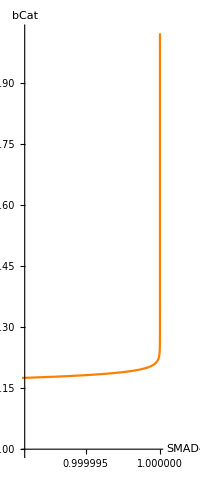

```mathematica
PlotTrajectory2D[1,{0,0,0},0,72,Orange]
```

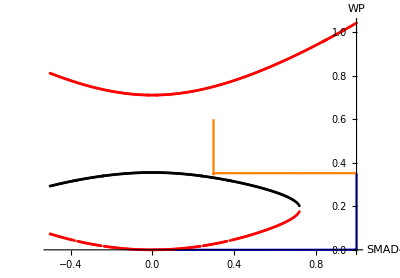

```mathematica
tmediachange = 24;
tF = 72;
concentrationfixedpointsBMP =1;
concentrationfixedpointsBMPafterMCH =0.3;
genestoplot = {1,2};
genestitles = {"SMAD4","WP"};
initcon = {0,0,0};
Show[PlotTrajectory2D[concentrationfixedpointsBMP,initcon,0,tmediachange,Blue],PlotTrajectory2D[concentrationfixedpointsBMPafterMCH,Evaluate[Table[y[i][tmediachange],{i,3}]/.SolveGRNODE[concentrationfixedpointsBMP,initcon,0,tmediachange]][[1]],tmediachange,tF,Orange],BifurcationSet[-0.5,1,0.005],PlotRange->  All,AxesLabel-> {genestitles[[genestoplot[[1]]]],genestitles[[genestoplot[[2]]]]}]
```

```mathematica
poly1=dSMAD4dt[BMP,SMAD4,WRNA,bCat] /.{BMP->0};
poly2 =dWRNAdt[BMP,SMAD4,WRNA,bCat] /.{BMP->0};
poly3=dbCatdt[BMP,SMAD4,WRNA,bCat] /.{BMP->0};
polys={poly1,poly2,poly3};
```

```mathematica
Ro1=Rts1[0]
```

{{0,0.711453,0.930253},{0,0,0},{0,0.355516,0.624657}}

```mathematica
i=3
```

3